```mathematica
SeedRandom[23787295];
t=0.45;
```

```mathematica
rpoints=RandomPoint[Rectangle[{-15,-2},{15,3}],10000];
Export[FileNameJoin[{NotebookDirectory[],"random_points.csv"}],rpoints];
```

```mathematica
rpoints=Import[FileNameJoin[{NotebookDirectory[],"random_points.csv"}]];
```

```mathematica
line1=Range[-15,15,30/500];
line2=Range[-2,3,5/500];
fpoints=Tuples[{line1,line2}];
```

```mathematica
kellycols=RGBColor/@({{230,25,75},{60,180,75},{255,225,25},{0,130,200},{245,130,48},{145,30,180},{70,240,240},{240,50,230},{210,245,60},{250,190,212},{0,128,128},{220,190,255},{170,110,40},{255,250,200},{128,0,0},{170,255,195},{128,128,0},{255,215,180},{0,0,128},{128,128,128},{255,255,255},{0,0,0}}/255)
```

{RGBColor[{Rational[46, 51], Rational[5, 51], Rational[5, 17]}],RGBColor[{Rational[4, 17], Rational[12, 17], Rational[5, 17]}],RGBColor[{1, Rational[15, 17], Rational[5, 51]}],RGBColor[{0, Rational[26, 51], Rational[40, 51]}],RGBColor[{Rational[49, 51], Rational[26, 51], Rational[16, 85]}],RGBColor[{Rational[29, 51], Rational[2, 17], Rational[12, 17]}],RGBColor[{Rational[14, 51], Rational[16, 17], Rational[16, 17]}],RGBColor[{Rational[16, 17], Rational[10, 51], Rational[46, 51]}],RGBColor[{Rational[14, 17], Rational[49, 51], Rational[4, 17]}],RGBColor[{Rational[50, 51], Rational[38, 51], Rational[212, 255]}],RGBColor[{0, Rational[128, 255], Rational[128, 255]}],RGBColor[{Rational[44, 51], Rational[38, 51], 1}],RGBColor[{Rational[2, 3], Rational[22, 51], Rational[8, 51]}],RGBColor[{1, Rational[50, 51], Rational[40, 51]}],RGBColor[{Rational[128, 255], 0, 0}],RGBColor[{Rational[2, 3], 1, Rational[13, 17]}],RGBColor[{Rational[128, 255], Rational[128, 255], 0}],RGBColor[{1, Rational[43, 51], Rational[12, 17]}],RGBColor[{0, 0, Rational[128, 255]}],RGBColor[{Rational[128, 255], Rational[128, 255], Rational[128, 255]}],RGBColor[{1, 1, 1}],RGBColor[{0, 0, 0}]}

## Square

```mathematica
1024/128
```

8

```mathematica
RunProcess[{"julia","-t 8","./squarePhases.jl","random_points.csv","100","128"},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
3705.091720 seconds (61.81 G allocations: 5.450 TiB, 40.60% gc time, 0.02% compilation time)
nothing
,StandardError→|>

```mathematica
RunProcess[{"julia","-t 8","./squarePhases.jl","random_points.csv","200","128"},ProcessDirectory->NotebookDirectory[]]
```

```mathematica
squareData=Import[FileNameJoin[{NotebookDirectory[],"out_100_128_random_points.csv"}]];
```

```mathematica
classedSquareData=StringJoin[ToString@Boole[#>t]&/@#]&/@squareData;
```

```mathematica
squareClassifier=Classify[rpoints->classedSquareData,Method->"NeuralNetwork",TargetDevice->"GPU"]
```

ClassifierFunction[…]

```mathematica
classedArray=Partition[squareClassifier[fpoints],Length[line1]];
```

```mathematica
lines=ContourPlot[{(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2==0.250368,(1-1/(1+ⅇ^(β μ)))^4(1-1/(1+ⅇ^(β (μ-1))))^4==0.407,1/128 (18+16 Cosh[β]+Cosh[2 β]) Sech[(β μ)/2]^4 Sech[1/2 (β-β μ)]^4==0.59274,(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4==0.59274},{μ,-2,3},{β,-15,15},AspectRatio->1,
ContourStyle->{Red,RGBColor[0.09,0.87,1],RGBColor[0.7,1,0],RGBColor[1,0.35,0]},LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"},PlotPoints->100];
```

```mathematica
Show[ArrayPlot[classedArray/.{"0000"->kellycols[[1]],"0001"->kellycols[[2]],"1000"->kellycols[[4]],"1010"->kellycols[[5]],"1100"->kellycols[[6]]},DataReversed->True,DataRange->{{-2,3},{-15,15}},AspectRatio->1],lines]
```

-Graphics-

```mathematica
ds2=(2-1/(1+ⅇ^(#1 #2))-ⅇ^#1/(ⅇ^#1+ⅇ^(#1 #2)))/2&@@@rpoints;
```

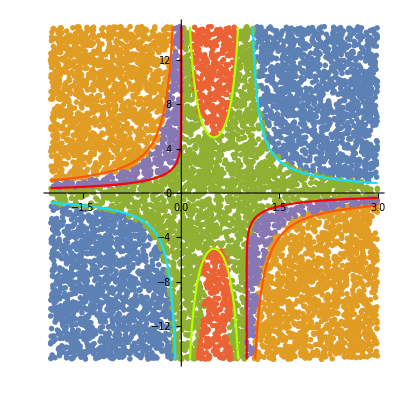

```mathematica
Show[ListPlot[{#1[[2]],#1[[1]]}&@@@#&/@GatherBy[Transpose[{rpoints,classedSquareData}],#[[2]]&],AspectRatio->1,PlotMarkers->{"OpenMarkers", Small}],lines]
```

### Edge hunting

```mathematica
squarePercDt=Boole[First[#]>t]&/@squareData;
```

```mathematica
sqEdgeClass=Classify[rpoints->squarePercDt,Method->"NeuralNetwork",TargetDevice->"GPU"]
```

ClassifierFunction[…]

```mathematica
sqEdgeArray=Partition[sqEdgeClass[fpoints],Length[line1]];
```

```mathematica
poss=Position[If[#==0,0,1]&/@#&/@ImageData[ImageConvolve[EdgeDetect[ImageCrop@Rasterize[ArrayPlot[sqEdgeArray,DataReversed->True,Frame->False],ImageSize->400]],BoxMatrix[5]]],1];
```

```mathematica
Length[poss]
```

10026

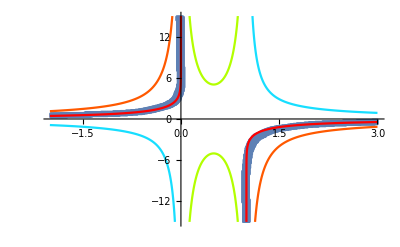

```mathematica
Show[ListPlot[{#2/512*5.-2.,-#1/512*30.+15}&@@@poss],lines]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sqEdge_points.csv"}],{-#1/512*30.+15,#2/512*5.-2.}&@@@poss]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\sqEdge_points.csv

```mathematica
RunProcess[{"julia","-t 8","./squarePhases.jl","sqEdge_points.csv","200","64"},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
4962.488119 seconds (84.68 G allocations: 6.488 TiB, 39.80% gc time, 0.02% compilation time)
nothing
,StandardError→|>

```mathematica
sqEdgeData=Import[FileNameJoin[{NotebookDirectory[],"out_200_64_sqEdge_points.csv"}]];
```

```mathematica
ds2=(2-1/(1+ⅇ^(#1 #2))-ⅇ^#1/(ⅇ^#1+ⅇ^(#1 #2)))/2&@@@({-#1/512*30.+15,#2/512*5.-2.}&@@@poss);
```

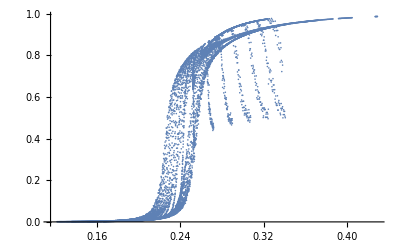

```mathematica
ListPlot[Transpose[{ds2,First/@sqEdgeData}]]
```

```mathematica
cl=FindClusters[Select[Transpose[{ds2,First/@sqEdgeData}],#[[1]]>0.250368&],Method->"Spectral"];
```

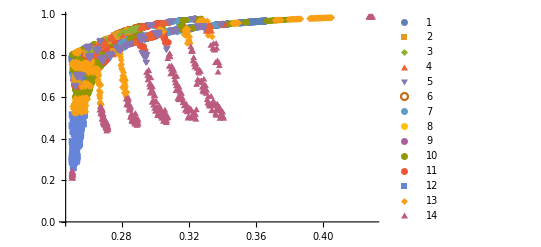

```mathematica
ListPlot[cl,PlotMarkers->{Automatic,Small},PlotLegends->Automatic]
```

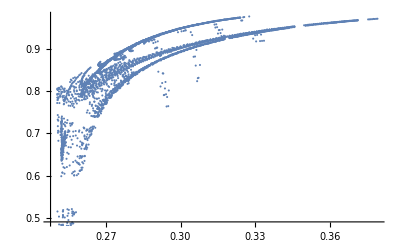

```mathematica
ListPlot[Join@@Drop[cl,{13,14}]]
```

```mathematica
nlm=NonlinearModelFit[Join@@Drop[cl,{14}],a Abs[p-0.250368]^β,{{a,1.2},{β,0.14}},p,ConfidenceLevel->0.99]
```

FittedModel[1.28107 Abs[-0.250368+p]^0.114598]

```mathematica
nlm=NonlinearModelFit[Select[Transpose[{ds2,First/@sqEdgeData}],#[[1]]>0.250368&],a (p-0.250368)^β,{{a,1.2},{β,0.14}},p,ConfidenceLevel->0.99]
```

FittedModel[1.19438 (-0.250368+p)^0.103095]

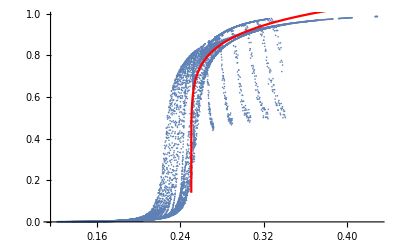

```mathematica
Show[ListPlot[Transpose[{ds2,First/@sqEdgeData}]],Plot[nlm[p],{p,0.250368,0.45},PlotStyle->Red,PlotRange->All]]
```

```mathematica
nlm["ParameterConfidenceIntervals"]
```

{{1.17153,1.21723},{0.0979263,0.108264}}

```mathematica
nlm2=NonlinearModelFit[Select[Transpose[{ds2,First/@sqEdgeData}],#[[1]]>0.250368&],a (p-0.250368)^(5/36),{{a,1.2}},p,ConfidenceLevel->0.99]
```

FittedModel[1.35314 (-0.250368+p)^(5/36)]

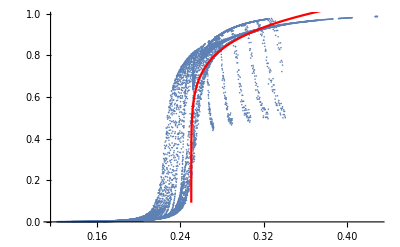

```mathematica
Show[ListPlot[Transpose[{ds2,First/@sqEdgeData}]],Plot[nlm2[p],{p,0.250368,0.45},PlotStyle->Red,PlotRange->All]]
```

### Percolation

#### β=20

```mathematica
FindRoot[((2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2==0.250368)/.β->20,{μ,0.}]
```

{μ→0.0001472}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],ToString[20]<>"sqMu_points.csv"}],Table[{20,μ},{μ,0.005,0.02,(0.02-(0.005))/100}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\20sqMu_points.csv

```mathematica
RunProcess[{"julia","-t 8","./squarePhases.jl",ToString[20]<>"sqMu_points.csv",200,1024},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
651.318469 seconds (11.61 G allocations: 924.035 GiB, 39.39% gc time, 0.12% compilation time)
nothing
,StandardError→|>

```mathematica
dt1=Transpose[{Last/@Import[FileNameJoin[{NotebookDirectory[],ToString[20]<>"sqMu_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_200_1024_20sqMu_points.csv"}]]}];
```

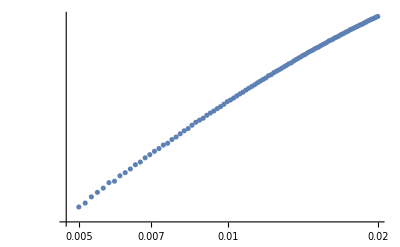

```mathematica
ListLogLogPlot[dt1]
```

```mathematica
nlm1=NonlinearModelFit[Select[dt1,#[[1]]>0.00014719969287001428&],a (μ-0.00014719969287001428)^e,{a,e},μ]
```

FittedModel[1.42154 (-0.0001472+μ)^0.102326]

```mathematica
nlm1["ParameterConfidenceIntervals"]
```

{{1.41423,1.42886},{0.10117,0.103482}}

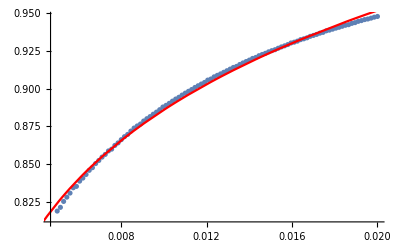

```mathematica
Show[ListPlot[dt1],Plot[nlm1[μ],{μ,-0.1,0.1},PlotStyle->Red,PlotRange->All]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sqMuplt_points.csv"}],Table[{20,μ},{μ,-0.1,0.1,(0.1-(-0.1))/100}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\sqMuplt_points.csv

```mathematica
RunProcess[{"julia","-t 8","./squarePhases.jl","sqMuplt_points.csv",100,64},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
 13.441254 seconds (245.46 M allocations: 20.327 GiB, 40.75% gc time, 5.66% compilation time)
nothing
,StandardError→|>

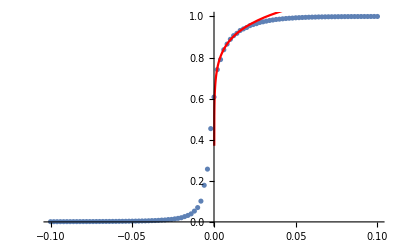

```mathematica
Show[ListPlot[Transpose[{Last/@Import[FileNameJoin[{NotebookDirectory[],"sqMuplt_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_100_64_sqMuplt_points.csv"}]]}]],Plot[nlm1[μ],{μ,-0.1,0.1},PlotStyle->Red,PlotRange->All]]
```

#### β=-20

```mathematica
FindRoot[((2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2==0.250368)/.β->-20,{μ,0.}]
```

{μ→0.999853}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],ToString[20]<>"sqMu2_points.csv"}],Table[{-20,μ},{μ,0.985,0.99,(0.99-(0.985))/100}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\20sqMu2_points.csv

```mathematica
RunProcess[{"julia","-t 8","./squarePhases.jl",ToString[20]<>"sqMu2_points.csv",200,1024},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
699.943791 seconds (11.57 G allocations: 909.952 GiB, 37.01% gc time, 0.11% compilation time)
nothing
,StandardError→|>

```mathematica
dt2=Transpose[{Last/@Import[FileNameJoin[{NotebookDirectory[],ToString[20]<>"sqMu2_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_200_1024_20sqMu2_points.csv"}]]}];
```

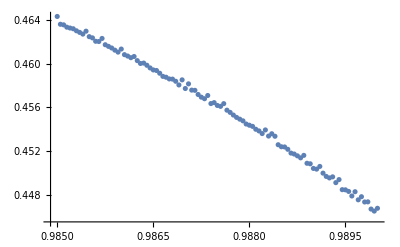

```mathematica
ListPlot[dt2]
```

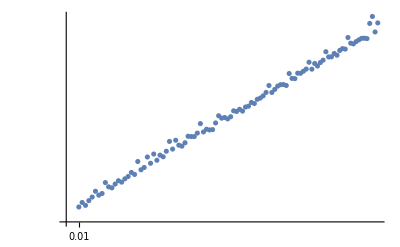

```mathematica
ListLogLogPlot[{1-#1,#2}&@@@dt2]
```

```mathematica
nlm2=NonlinearModelFit[dt2,a (1-μ)^e,{a,e},μ]
```

FittedModel[0.702148 (1-μ)^0.0983475]

```mathematica
nlm2["ParameterConfidenceIntervals"]
```

{{0.697898,0.706398},{0.0969992,0.0996958}}

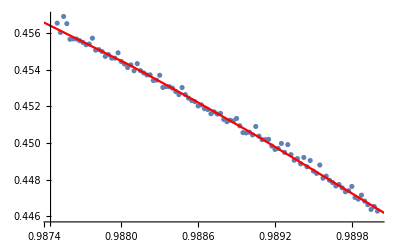

```mathematica
Show[ListPlot[dt2],Plot[nlm2[μ],{μ,0.8,1.2},PlotStyle->Red,PlotRange->All]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sqMuplt2_points.csv"}],Table[{-20,μ},{μ,0.9,1.1,(1.1-(0.9))/100}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\sqMuplt2_points.csv

```mathematica
RunProcess[{"julia","-t 8","./squarePhases.jl","sqMuplt2_points.csv",100,64},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
 12.631236 seconds (244.12 M allocations: 20.132 GiB, 42.54% gc time, 5.87% compilation time)
nothing
,StandardError→|>

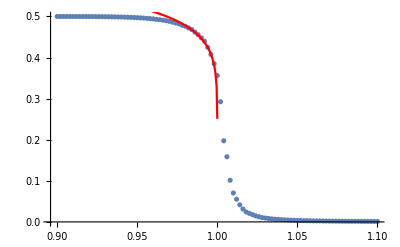

```mathematica
Show[ListPlot[Transpose[{Last/@Import[FileNameJoin[{NotebookDirectory[],"sqMuplt2_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_100_64_sqMuplt2_points.csv"}]]}]],Plot[nlm2[μ],{μ,0,2},PlotStyle->Red,PlotRange->All]]
```

#### μ=-5

```mathematica
FindRoot[((2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2==0.250368)/.μ->-5,{β,0.}]
```

{β→0.199844}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sqBeta_points.csv"}],Table[{β,-5.},{β,0.11,0.15,(0.15-(0.11))/100}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\sqBeta_points.csv

```mathematica
RunProcess[{"julia","-t 8","./squarePhases.jl","sqBeta_points.csv",200,1024},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
774.317598 seconds (12.56 G allocations: 1004.580 GiB, 36.96% gc time, 0.10% compilation time)
nothing
,StandardError→|>

```mathematica
dt4=Transpose[{First/@Import[FileNameJoin[{NotebookDirectory[],"sqBeta_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_200_1024_sqBeta_points.csv"}]]}];
```

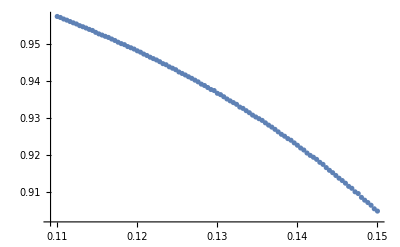

```mathematica
ListPlot[dt4]
```

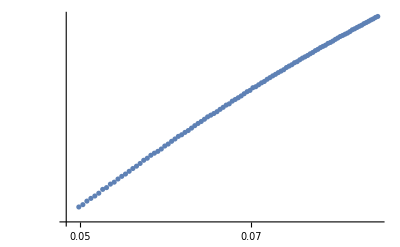

```mathematica
ListLogLogPlot[{0.19984427975213995-#1,#2}&@@@dt4]
```

```mathematica
nlm4=NonlinearModelFit[Select[dt4,#[[1]]<0.19984427975213995&],a ((0.19984427975213995)-β)^e,{a,e},β]
```

FittedModel[1.20839 (0.199844-β)^0.0959853]

```mathematica
nlm4["ParameterConfidenceIntervals"]
```

{{1.20561,1.21117},{0.0951261,0.0968444}}

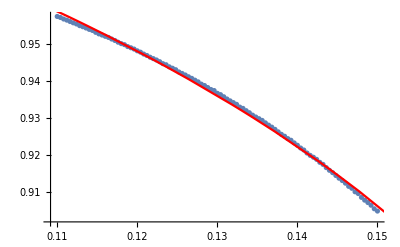

```mathematica
Show[ListPlot[dt4],Plot[nlm4[β],{β,0,1},PlotStyle->Red,PlotRange->All]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sqBetaplt_points.csv"}],Table[{β,-5.},{β,0.,0.4,(0.4-(0.))/100}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\sqBetaplt_points.csv

```mathematica
RunProcess[{"julia","-t 8","./squarePhases.jl","sqBetaplt_points.csv",100,64},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
 12.820835 seconds (240.10 M allocations: 19.497 GiB, 41.79% gc time, 6.40% compilation time)
nothing
,StandardError→|>

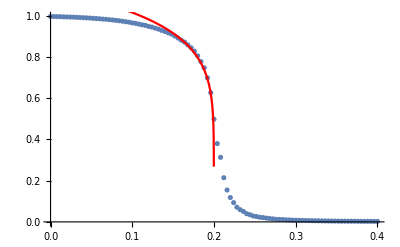

```mathematica
Show[ListPlot[Transpose[{First/@Import[FileNameJoin[{NotebookDirectory[],"sqBetaplt_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_100_64_sqBetaplt_points.csv"}]]}]],Plot[nlm4[β],{β,0,1},PlotStyle->Red,PlotRange->All]]
```

#### μ=5

```mathematica
FindRoot[((2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2==0.250368)/.μ->5,{β,0.}]
```

{β→-0.24453}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sqBeta2_points.csv"}],Table[{β,5.},{β,-0.2,-0.24,(-0.24-(-0.2))/100}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\sqBeta2_points.csv

```mathematica
RunProcess[{"julia","-t 8","./squarePhases.jl","sqBeta2_points.csv",200,1024},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
810.624557 seconds (13.12 G allocations: 1.045 TiB, 37.87% gc time, 0.09% compilation time)
nothing
,StandardError→|>

```mathematica
dt5=Transpose[{First/@Import[FileNameJoin[{NotebookDirectory[],"sqBeta2_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_200_1024_sqBeta2_points.csv"}]]}];
```

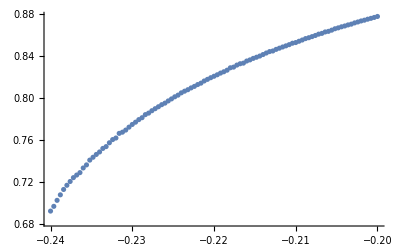

```mathematica
ListPlot[dt5]
```

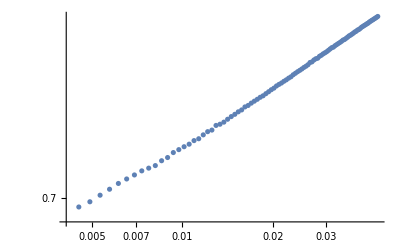

```mathematica
ListLogLogPlot[{#1+0.24452964855598716,#2}&@@@dt5]
```

```mathematica
nlm5=NonlinearModelFit[Select[dt5,#[[1]]>-0.24452964855598716&],a ((0.24452964855598716)+β)^e,{a,e},β]
```

FittedModel[1.22195 (0.24453+β)^0.107006]

```mathematica
nlm5["ParameterConfidenceIntervals"]
```

{{1.21819,1.22572},{0.106201,0.10781}}

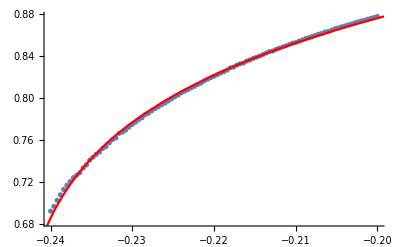

```mathematica
Show[ListPlot[dt5],Plot[nlm5[β],{β,-1,0},PlotStyle->Red,PlotRange->All]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sqBetaplt2_points.csv"}],Table[{β,5.},{β,-0.5,0.,(0.-(-0.5))/100}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\sqBetaplt2_points.csv

```mathematica
RunProcess[{"julia","-t 8","./squarePhases.jl","sqBetaplt2_points.csv",100,64},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
 12.816031 seconds (241.02 M allocations: 19.594 GiB, 41.60% gc time, 6.18% compilation time)
nothing
,StandardError→|>

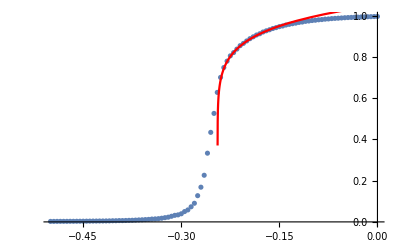

```mathematica
Show[ListPlot[Transpose[{First/@Import[FileNameJoin[{NotebookDirectory[],"sqBetaplt2_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_100_64_sqBetaplt2_points.csv"}]]}]],Plot[nlm5[β],{β,-1,0},PlotStyle->Red,PlotRange->All]]
```

## Cube

```mathematica
RunProcess[{"julia","-t 8","./cubePhases.jl","random_points.csv","10","128"},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
647.383434 seconds (8.76 G allocations: 1.290 TiB, 38.70% gc time, 0.12% compilation time)
nothing
,StandardError→|>

```mathematica
RunProcess[{"julia","-t 8","./cubePhases.jl","random_points.csv","20","128"},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
5951.403412 seconds (65.25 G allocations: 8.605 TiB, 40.25% gc time, 0.01% compilation time)
nothing
,StandardError→|>

```mathematica
RunProcess[{"julia","-t 8","./cubePhases.jl","random_points.csv","40","128"},ProcessDirectory->NotebookDirectory[]]
```

$Aborted

```mathematica
cubeData=Import[FileNameJoin[{NotebookDirectory[],"out_20_128_random_points.csv"}]];
```

```mathematica
classedCubeData=StringJoin[ToString@Boole[#>t]&/@#]&/@cubeData;
```

```mathematica
cubeClassifier=Classify[rpoints->classedCubeData,Method->"NeuralNetwork",TargetDevice->"GPU"]
```

ClassifierFunction[…]

```mathematica
classedCubeArray=Partition[cubeClassifier[fpoints],Length[line1]];
```

```mathematica
Counts[Flatten@classedCubeArray]
```

<|1000000000000000000000000010→51147,1000000000000000000000000000→115006,1000000000000000000010000000→8609,0000000000000000000000000000→8464,0000000000000000000000000001→51177,1000000010000000000000000000→1892,1000000000000000001000000000→7484,1000001000000000000000000000→7222|>

```mathematica
Length[DeleteDuplicates[Flatten@classedCubeArray]]
```

8

```mathematica
cols=#1->#2&@@@Transpose[{#,Take[kellycols,Length[#]]}&@DeleteDuplicates[Flatten@classedCubeArray]];
```

```mathematica
ArrayPlot[classedCubeArray/.cols,DataReversed->True,DataRange->{{-2,3},{-15,15}},AspectRatio->1]
```

-Graphics-

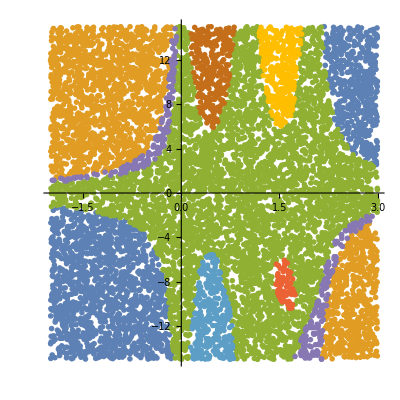

```mathematica
ListPlot[{#1[[2]],#1[[1]]}&@@@#&/@GatherBy[Transpose[{rpoints,classedCubeData}],#[[2]]&],AspectRatio->1,PlotMarkers->{"OpenMarkers", Small}]
```

```mathematica
Show[ArrayPlot[classedCubeArray/.cols,DataReversed->True,DataRange->{{-2,3},{-15,15}},AspectRatio->1],ListPlot[{#1[[2]],#1[[1]]}&@@@#&/@GatherBy[Transpose[{rpoints,classedCubeData}],#[[2]]&],AspectRatio->1,PlotMarkers->{"OpenMarkers", Small}]]
```

-Graphics-

## Hex

```mathematica
RunProcess[{"julia","-t 8","./hexPhases.jl","random_points.csv","35","128"},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
1973.033315 seconds (21.90 G allocations: 2.426 TiB, 64.15% gc time, 0.03% compilation time)
nothing
,StandardError→|>

```mathematica
RunProcess[{"julia","-t 8","./hexPhases.jl","random_points.csv","70","128"},ProcessDirectory->NotebookDirectory[]]
```

<|ExitCode→0,StandardOutput→8
6012.720387 seconds (82.67 G allocations: 9.088 TiB, 46.15% gc time, 0.01% compilation time)
nothing
,StandardError→|>

```mathematica
RunProcess[{"julia","-t 8","./hexPhases.jl","random_points.csv","140","128"},ProcessDirectory->NotebookDirectory[]]
```

```mathematica
hexData=Import[FileNameJoin[{NotebookDirectory[],"out_70_128_random_points.csv"}]];
```

```mathematica
classedHexData=StringJoin[ToString@Boole[#>t]&/@#]&/@hexData;
```

```mathematica
hexClassifier=Classify[rpoints->classedHexData,Method->"NeuralNetwork",TargetDevice->"GPU"]
```

ClassifierFunction[…]

```mathematica
classedHexArray=Partition[hexClassifier[fpoints],Length[line1]];
```

```mathematica
Counts[Flatten@classedHexArray]
```

<|10000000000010→59089,10000000000000→85530,10000000010000→19674,10010000000000→12093,00000000000000→14624,00000000000001→59991|>

```mathematica
Length[DeleteDuplicates[Flatten@classedHexArray]]
```

6

```mathematica
colsH=#1->#2&@@@Transpose[{#,Take[kellycols,Length[#]]}&@DeleteDuplicates[Flatten@classedHexArray]];
```

```mathematica
ArrayPlot[classedHexArray/.colsH,DataReversed->True,DataRange->{{-2,3},{-15,15}},AspectRatio->1]
```

-Graphics-

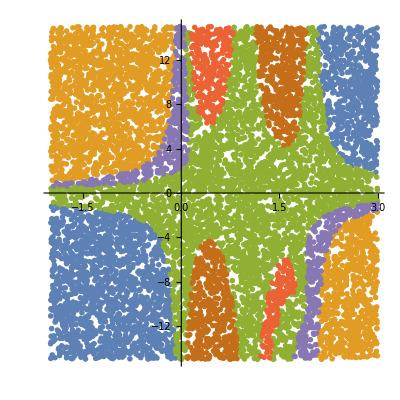

```mathematica
ListPlot[{#1[[2]],#1[[1]]}&@@@#&/@GatherBy[Transpose[{rpoints,classedHexData}],#[[2]]&],AspectRatio->1,PlotMarkers->{"OpenMarkers", Medium}]
```

```mathematica
Show[ArrayPlot[classedHexArray/.colsH,DataReversed->True,DataRange->{{-2,3},{-15,15}},AspectRatio->1],ListPlot[{#1[[2]],#1[[1]]}&@@@#&/@GatherBy[Transpose[{rpoints,classedHexData}],#[[2]]&],AspectRatio->1,PlotMarkers->{"OpenMarkers", Small}]]
```

-Graphics-